```mathematica
δ1={1,0};
δ2=0.5{1,√3};
```

```mathematica
Ltp=20;
ns=Partition[Flatten[Table[{n1,n2},{n1,-Ltp,Ltp},{n2,-Ltp,Ltp}]],2];
```

```mathematica
latt=(#[[1]]*δ1+#[[2]]*δ2)&/@ns;
```

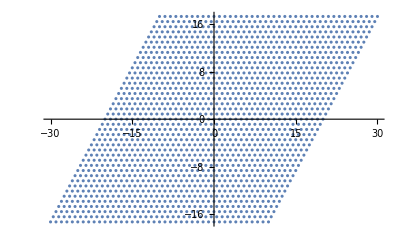

```mathematica
ListPlot[latt]
```

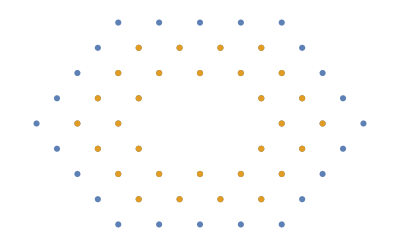

```mathematica
L1=1.6;L2=4;L3=1.2;L4=3;
slatt=DeleteCases[If[L1≤Norm[#]≤L2,#]&/@latt,Null];
dlatt=DeleteCases[If[L3≤Norm[#]≤L4,#]&/@latt,Null];
ListPlot[{slatt,dlatt},Axes->False]
```

```mathematica
S1[kx_,ky_]=Sum[Exp[ⅈ*kx*(s2[[1]]-s1[[1]])]Exp[ⅈ*ky*(s2[[2]]-s1[[2]])],{s1,slatt},{s2,slatt}];
S2[kx_,ky_]=Sum[Exp[ⅈ*kx*(s2[[1]]-s1[[1]])]Exp[ⅈ*ky*(s2[[2]]-s1[[2]])],{s1,dlatt},{s2,dlatt}];
```

```mathematica
R=4.0;
R1=2;
R2=1.;
qs=q/.NSolve[{BesselJ[1,q R π]/(q R π)==0,0<q<2},q,Reals]
```

{0.304917,0.558283,0.809579,1.06027,1.31069,1.56098,1.81119}

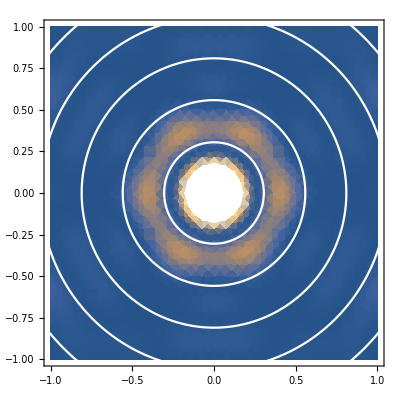

```mathematica
Show[DensityPlot[Re[S1[kx*π,ky*π]],{kx,-1,1},{ky,-1,1},PlotRange->{0,500}],ParametricPlot[#*{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},PlotStyle->White]&/@qs]
```

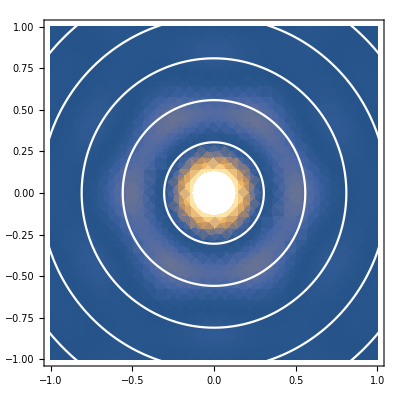

```mathematica
Show[DensityPlot[Abs[S2[kx*π,ky*π]],{kx,-1,1},{ky,-1,1},PlotRange->{0,500}],ParametricPlot[#*{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},PlotStyle->White]&/@qs]
```

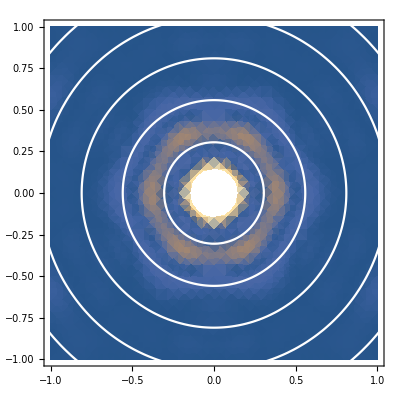

```mathematica
Show[DensityPlot[Re[Abs[S1[kx*π,ky*π]-S2[kx*π,ky*π]]],{kx,-1,1},{ky,-1,1},PlotRange->{0,500}],ParametricPlot[#*{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},PlotStyle->White]&/@qs]
```